```mathematica
data=
Import["/Users/epersico/Google Drive/GitHub/Map Files/Good Data/201706/run3/widths/m_1_n_2_widths.out","Table"]
```

{{0.003,0.0005},{0.004,0.0005},{0.005,0.00075},{0.006,0.00075},{0.007,0.001},{0.008,0.00125},{0.009,0.00125},{0.01,0.0015},{0.011,0.00175},{0.012,0.00175},{0.013,0.002},{0.014,0.002},{0.015,0.00225},{0.016,0.0025},{0.017,0.0025},{0.018,0.00275},{0.019,0.003},{0.02,0.003},{0.021,0.00325},{0.022,0.0035},{0.023,0.0035},{0.024,0.00375},{0.025,0.004},{0.026,0.004},{0.027,0.00425},{0.028,0.00425},{0.029,0.0045},{0.03,0.00475},{0.031,0.00475},{0.032,0.005},{0.033,0.00525},{0.034,0.00525},{0.035,0.0055},{0.036,0.00575},{0.037,0.00575},{0.038,0.006},{0.039,0.00625},{0.04,0.00625},{0.041,0.0065},{0.042,0.00675},{0.043,0.00675},{0.044,0.007},{0.045,0.007},{0.046,0.00725},{0.047,0.0075},{0.048,0.0075},{0.049,0.00775},{0.05,0.008},{0.051,0.008},{0.052,0.00825},{0.053,0.0085},{0.054,0.0085},{0.055,0.00875},{0.056,0.009},{0.057,0.009},{0.058,0.00925},{0.059,0.0095},{0.06,0.0095},{0.061,0.00975},{0.062,0.01},{0.063,0.01},{0.064,0.01025},{0.065,0.0105},{0.066,0.0105},{0.067,0.01075},{0.068,0.011},{0.069,0.011},{0.07,0.01125},{0.071,0.0115},{0.072,0.0115},{0.073,0.01175},{0.074,0.01175},{0.075,0.012},{0.076,0.01225},{0.077,0.01225},{0.078,0.0125},{0.079,0.01275},{0.08,0.01275},{0.081,0.013},{0.082,0.01325},{0.083,0.01325},{0.084,0.0135},{0.085,0.01375},{0.086,0.01375},{0.087,0.014},{0.088,0.01425},{0.089,0.01425},{0.09,0.0145},{0.091,0.01475},{0.092,0.01475},{0.093,0.015},{0.094,0.01525},{0.095,0.01525},{0.096,0.0155},{0.097,0.01575},{0.098,0.01575},{0.099,0.016},{0.1,0.01625}}

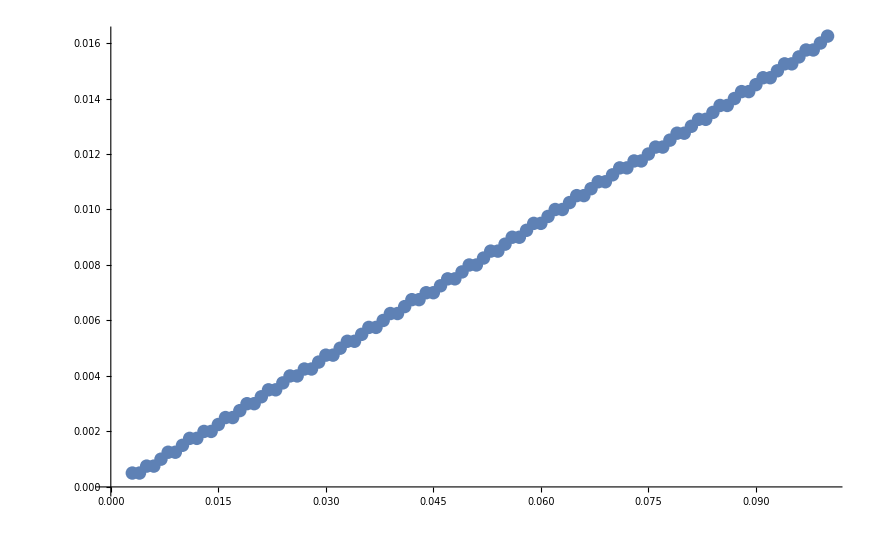

```mathematica
ListPlot[data]
```

```mathematica
logdata = data;
logdata[[All,2]] = Log[logdata[[All,2]]];
```

```mathematica
0.35/100 
0.1/%
```

0.0035

28.5714

-6.05922+14.451 x

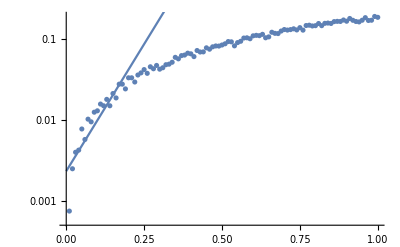

```mathematica
line1 = Fit[logdata[[1;;20,All]],{1,x},x]
Show[ListLogPlot[data],Plot[line1,{x,0,1}]]
```

FittedModel[-0.0000585458+0.170115 x^1.02075]

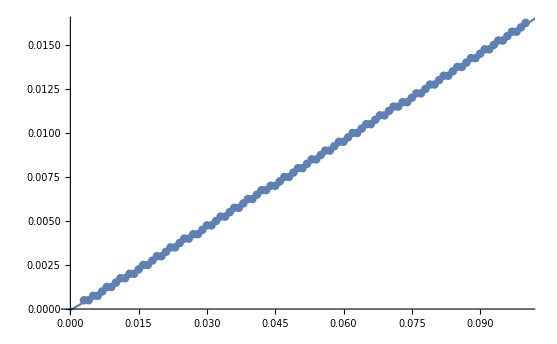

```mathematica
nlm=NonlinearModelFit[data[[All,All]],a +b x^c,{a,b,c},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,1}]]
```

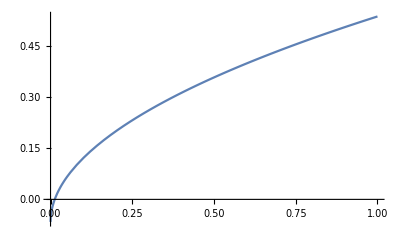

```mathematica
Plot[nlm[x],{x,0,1}]
```